```mathematica
computeAabbPoints[min_,max_]:=(
pts={};
For[i=0,i<8,i++,
pt={If[BitAnd[i,1]>0,min[[1]],max[[1]]],
If[BitAnd[i,2]>0,min[[2]],max[[2]]],
If[BitAnd[i,4]>0,min[[3]],max[[3]]],1};
AppendTo[pts,pt];
];
pts
);


toDrawPoints[pts_]:=(
appfunc[pt_]:=Point[{pt[[1]],pt[[2]],pt[[3]]}];
Map[appfunc,pts]
);

toFrustumLines[inpts_]:=(
extract3coords[pt_]:={pt[[1]],pt[[2]],pt[[3]]};
pts=Map[extract3coords,inpts];
{
Line[{pts[[1]],pts[[2]]}],
Line[{pts[[1]],pts[[3]]}],
Line[{pts[[2]],pts[[4]]}],
Line[{pts[[3]],pts[[4]]}],

Line[{pts[[5]],pts[[6]]}],
Line[{pts[[5]],pts[[7]]}],
Line[{pts[[6]],pts[[8]]}],
Line[{pts[[7]],pts[[8]]}],

Line[{pts[[1]],pts[[5]]}],
Line[{pts[[2]],pts[[6]]}],
Line[{pts[[3]],pts[[7]]}],
Line[{pts[[4]],pts[[8]]}]
}
);

transformBox[pts_,transform_]:=(
result={};
For[i=0,i<8,i++,
pt=transform.pts[[i+1]];
pt/=pt[[4]];
AppendTo[result,pt];
];
result
)
```

```mathematica
{minx,miny,minz,maxx,maxy,maxz}
{Slider[Dynamic[minx],{-70,70,1}],Dynamic[minx]}
{Slider[Dynamic[miny],{-70,70,1}],Dynamic[miny]}
{Slider[Dynamic[minz],{-70,70,1}],Dynamic[minz]}
{Slider[Dynamic[maxx],{-70,70,1}],Dynamic[maxx]}
{Slider[Dynamic[maxy],{-70,70,1}],Dynamic[maxy]}
{Slider[Dynamic[maxz],{65,70,0.1}],Dynamic[maxz]}
Dynamic[
boxmin={minx,miny,minz};
boxmax={maxx,maxy,maxz};
bboxptsWorld=computeAabbPoints[boxmin, boxmax];

frustum={{1.63793051,-9.07602725*10^-7,0.0939856470,-2.02233100},{0.0258359760,-2.88158321,-0.450283080,16.5108833},{-0.00628861552,-0.0171818640,0.109594382,6.96916246},{0.0565975122,0.154636696,-0.986348987,37.2775154}};
bboxpts=transformBox[bboxptsWorld, frustum];

fruMin={-1,-1,0};
fruMax={1,1,1};
frupts=computeAabbPoints[fruMin, fruMax];
fruptsWorld=transformBox[frupts, Inverse[frustum]];

arrows={Red,Arrowheads[0.01],Arrow[{{0,0,0},{5,0,0}}],Green,Arrow[{{0,0,0},{0,5,0}}],Blue,Arrow[{{0,0,0},{0,0,5}}]};
{Graphics3D[{toFrustumLines[bboxptsWorld],Red,toFrustumLines[fruptsWorld],arrows},ViewVector->{100,10,10}],Graphics3D[{toFrustumLines[bboxpts],Red,toFrustumLines[frupts]},ViewVector->{{2,-2,0},{0,0,0}}]}]
Dynamic[bboxpts]
```

{-70,-1,-70,68,0,70.}

{,}

{,}

{,}

«3 more identical outputs»

```mathematica
func[maxz_]:=
(boxmin={minx,miny,minz};
boxmax={maxx,maxy,maxz};
bboxptsWorld=computeAabbPoints[boxmin, boxmax];

frustum={{1.63793051,-9.07602725*10^-7,0.0939856470,-2.02233100},{0.0258359760,-2.88158321,-0.450283080,16.5108833},{-0.00628861552,-0.0171818640,0.109594382,6.96916246},{0.0565975122,0.154636696,-0.986348987,37.2775154}};
bboxpts=transformBox[bboxptsWorld, frustum];

fruMin={-1,-1,0};
fruMax={1,1,1};
frupts=computeAabbPoints[fruMin, fruMax];
fruptsWorld=transformBox[frupts, Inverse[frustum]];

bboxpts[[1,1]]
)
```

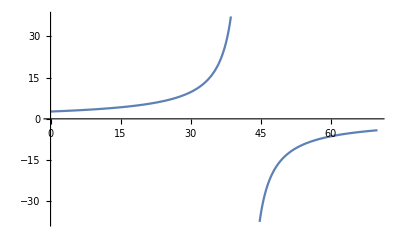

{68,0,45,1}

{113.586,-1.99501,11.4733,-3.25956}

{-34.8471,0.612049,-3.51989,1.}

```mathematica
Plot[func[x],{x,0,70}]

boxmin={minx,miny,minz};
boxmax={maxx,maxy,45};
bboxptsWorld=computeAabbPoints[boxmin, boxmax];
pt=bboxptsWorld[[1]]
transformed=frustum.pt
transformed/transformed[[4]]
```

```mathematica
pointsWorld={{68,0,45}};
frustum={{1.63793051,-9.07602725*10^-7,0.0939856470,-2.02233100},{0.0258359760,-2.88158321,-0.450283080,16.5108833},{-0.00628861552,-0.0171818640,0.109594382,6.96916246},{0.0565975122,0.154636696,-0.986348987,37.2775154}};


mapfunc[pt_]:=(
result=frustum.{pt[[1]],pt[[2]],pt[[3]],1};
result/=result[[4]];
{result[[1]],result[[2]],result[[3]]}
);
points=Map[mapfunc,pointsWorld];

fruMin={-1,-1,0};
fruMax={1,1,1};
frupts=computeAabbPoints[fruMin, fruMax];
fruptsWorld=transformBox[frupts, Inverse[frustum]];

arrows={Red,Arrowheads[0.01],Arrow[{{0,0,0},{5,0,0}}],Green,Arrow[{{0,0,0},{0,5,0}}],Blue,Arrow[{{0,0,0},{0,0,5}}]};
{Graphics3D[{toDrawPoints[pointsWorld],Red,toFrustumLines[fruptsWorld],arrows},ViewVector->{100,10,10}],Graphics3D[{toDrawPoints[points],Red,toFrustumLines[frupts]},ViewVector->{{20,-2,0},{0,0,0}}]}
```

{-Graphics3D-,-Graphics3D-}